```mathematica
f1[x_]:=x^.4+0.1-x
```

```mathematica
sols1=x/.Solve[f1[x]==0,x][[1]]
```

1.16184

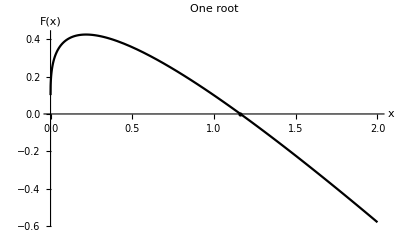

```mathematica
g1=Plot[{f1[x]},{x,0,2},Ticks->None,AxesLabel->{"x","F(x)"},Epilog->{PointSize[Large],Point[{sols1,f1[sols1]}]},PlotStyle->Black,PlotLabel->"One root"]
```

```mathematica
f2[x_]:=-3*x^1.1+x^0.5+.1+x-0.2
```

```mathematica
sols2=x/.Solve[f2[x]==0,x]
```

{0.0124675,0.246642}

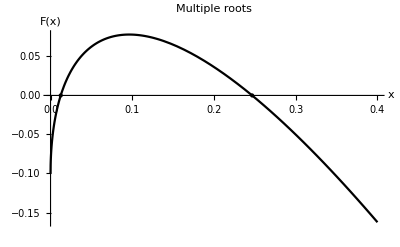

```mathematica
g2=Plot[{f2[x]},{x,0,0.4},AxesOrigin->{0,0},Ticks->None,AxesLabel->{"x","F(x)"},Epilog->{PointSize[Large],Point[{#,f2[#]}&/@sols2]},PlotStyle->Black,PlotLabel->"Multiple roots"]
```

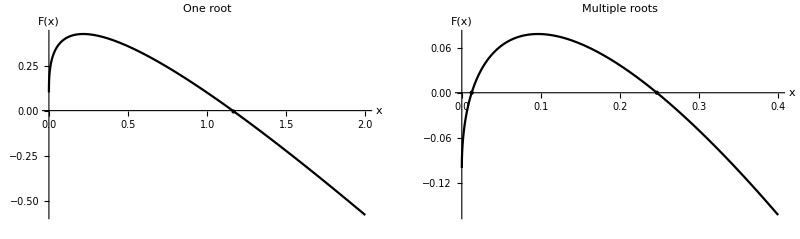

```mathematica
pl1=GraphicsRow[{g1,g2}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/math_app/roots.png",pl1]
```

/home/eric/eric-roca.github.io/static/img/math_app/roots.png